### Bi2Se3

#### TB

```mathematica
<<TopoTB`
```

```mathematica
SetDirectory[FileNameTake[NotebookFileName[],{1,-2}]];
(*Import wannier90_hr.dat file*)
wannier90hr=Import["wannier90_hr.dat","Table"];
(*Import POSCAR files, or write directly to a, b, and c without importing them*)
poscar=Import["POSCAR","Table"];
(*Import WFcenter*)
wfcentre=Import["WFcentre.txt","Table"];
(*Fermi level*)
efermi=4.4182;
a=poscar[[3]];b=poscar[[4]];c=poscar[[5]];
lat={a,b,c};
```

```mathematica
dsLattice=Wannier90hr[wannier90hr,lat,{kx,ky,kz}]
dsAtom=Wannier90hr[wannier90hr,lat,{kx,ky,kz},2,wfcentre]
```

```mathematica
HLattice=Normal[dsLattice[7]];
HLattice//TraditionalForm
HLattice/.{kx->1,ky->1,kz->1}//TraditionalForm
```

```mathematica
HAtom=Normal[dsAtom[7]];
HAtom//TraditionalForm
HAtom/.{kx->1,ky->1,kz->1}//TraditionalForm
```

#### Band

```mathematica
Clear[h]
h[{kx_,ky_,kz_}]=HLattice;
G={0,0,0};Z={0,0,0.5};F={0.5,0.5,0};L={0.5,0,0};
klabel={"Γ","Z","F","Γ","L"};
ds1=HSPBand[h,lat,{{G,Z,10},{Z,F,30},{F,G,30},{G,L,30}},klabel,efermi]
```

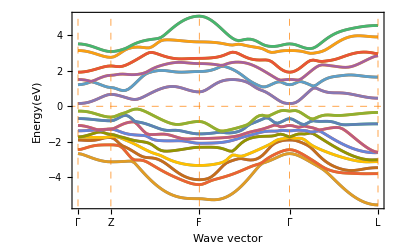

```mathematica
ds1[5]
```

```mathematica
Clear[h]
h[{kx_,ky_,kz_}]=HAtom;
G={0,0,0};Z={0,0,0.5};F={0.5,0.5,0};L={0.5,0,0};
klabel={"Γ","Z","F","Γ","L"};
ds2=HSPBand[h,lat,{{G,Z,10},{Z,F,30},{F,G,30},{G,L,30}},klabel,efermi]
```

```mathematica
ds2[5]
```

-Graphics-

#### Z2

```mathematica
Clear[h]
h[{kx_,ky_,kz_}]=HLattice;
lat
bnd=Table[i,{i,1,18}]
UT=KroneckerProduct[I*PauliMatrix[2],IdentityMatrix[Normal[dsLattice[1]]/2]];
```

{{-2.069,-3.58361,0.},{2.069,-3.58361,0.},{0.,2.38908,9.54667}}

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18}

```mathematica
{ds1=Z2NumberCalc[h,lat,bnd,UT,1]}//AbsoluteTiming
{ds2=Z2NumberCalc[h,lat,bnd,UT,2]}//AbsoluteTiming
{ds3=Z2NumberCalc[h,lat,bnd,UT,3]}//AbsoluteTiming
{ds4=Z2NumberCalc[h,lat,bnd,UT,4]}//AbsoluteTiming
{ds5=Z2NumberCalc[h,lat,bnd,UT,5]}//AbsoluteTiming
{ds6=Z2NumberCalc[h,lat,bnd,UT,6]}//AbsoluteTiming
```

{35.1848,{}}

{35.6616,{}}

{35.8005,{}}

{35.5924,{}}

{35.6968,{}}

{35.7654,{}}

```mathematica
{ds1[3],ds2[3],ds3[3],ds4[3],ds5[3],ds6[3]}
```

{1,0,1,0,1,0}